MAT120
Assignment 1

5.  a)

2

-4 x+x^3

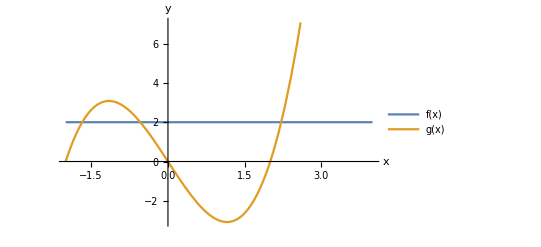

```mathematica
f[x_]=2
g[x_]=x^3-4x
Plot[{f[x],g[x]},{x,-2,4},
AxesLabel->{"x","y"},
PlotLegends->"Expressions"]
```

b) The limits of integration are

```mathematica
Solve[f[x]==g[x]&&-2≤ x≤ 4,x]//N
```

{{x→-1.67513},{x→-0.539189},{x→2.21432}}

c) For x axis,the area bounded by two curves are ∫_(left limit)^(right limit) (top curve - bottom curve)ⅆx

```mathematica
∫_-1.6751308705666461^-0.5391888728108891 (g[x]-f[x])ⅆx +∫_-0.5391888728108891^2.2143197433775352 (f[x]-g[x])ⅆx//N
```

9.55418

So, Area = 9.55418 unit^2